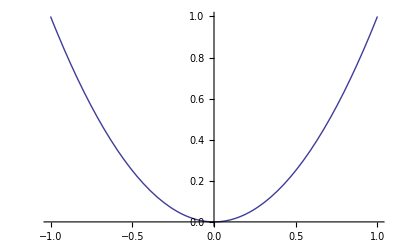

```mathematica
Plot[x^2,{x,-1,1}]
```

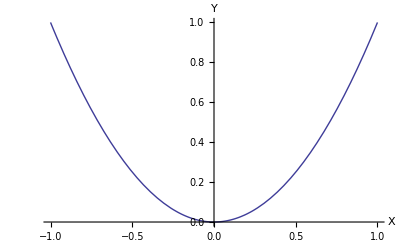

```mathematica
Plot[x^2,{x,-1,1},AxesLabel-> {"X","Y"}]
```

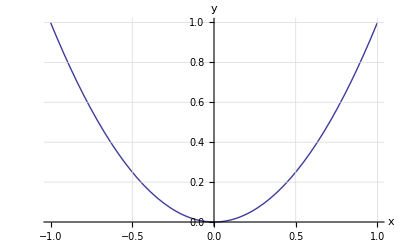

```mathematica
Plot[x^2,{x,-1,1},AxesLabel-> {"x","y"},GridLines-> {{-1.5,-.5,.5,1.0},{.2,.4,.6,.8,1}}]
```

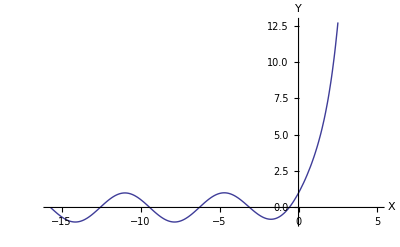

```mathematica
Plot[E^x+Sin[x],{x,-5Pi,5},AxesLabel-> {"X","Y"}]
```

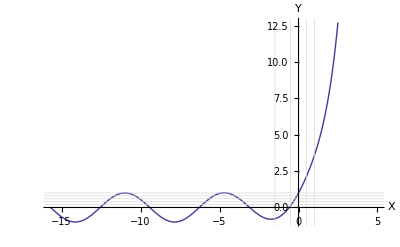

```mathematica
Plot[E^x+Sin[x],{x,-5Pi,5},AxesLabel-> {"X","Y"},GridLines-> {{-1.5,-0.5,0.5,1.0},{0.2,0.4,0.6,0.8,1}}]
```

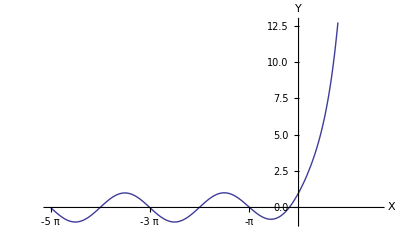

```mathematica
Plot[E^x+Sin[x],{x,-5Pi,5},AxesLabel-> {"X","Y"},Ticks-> {{-5Pi,-4Pi,-3Pi,-2Pi,-Pi,Pi,2Pi},Automatic}]
```

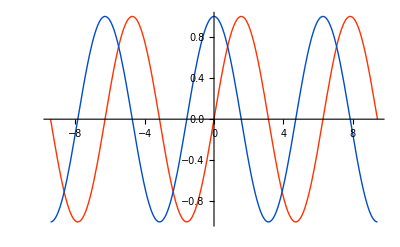

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3Pi,3Pi},PlotStyle-> {RGBColor[1,0.2,0],RGBColor[0,0.3,0.8]}]
```

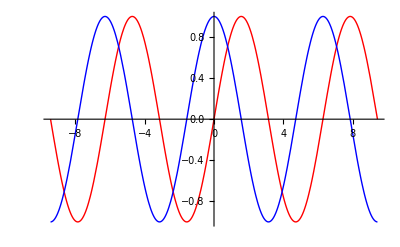

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3Pi,3Pi},PlotStyle->{Red,Blue}]
```

```mathematica
<<"PlotLegends`"
```

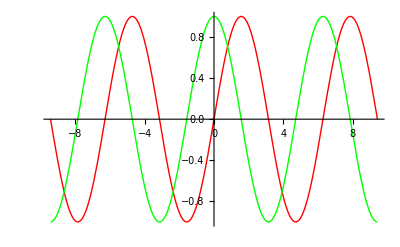

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3Pi,3Pi},PlotStyle->{Red,Green},PlotLegend-> {"Y=Sin X","Y=Cos X"}]
```

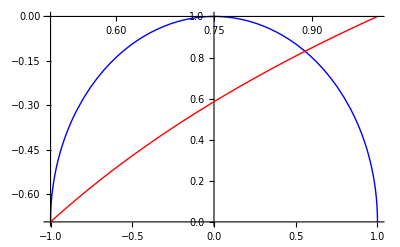

```mathematica
Show[{Plot[{Sqrt[1-x^2]},{x,-1,1},PlotStyle-> Blue,PlotLegend-> {"Y=√(1-x^2)"}]},{Plot[Log[x],{x,0.5,1},PlotStyle-> Red,PlotLegend-> {"Y=ln X"}]}]
```

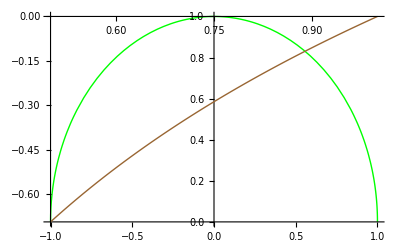

```mathematica
Show[{Plot[{Sqrt[1-x^2]},{x,-1,1},PlotStyle-> Green,PlotLegend-> {"Y=√(1-x^2)"},LegendPosition-> {1,0.3}]},{Plot[Log[x],{x,0.5,1},PlotStyle-> Brown,PlotLegend-> {"Y=ln X"},LegendPosition-> {1,0}]}]
```

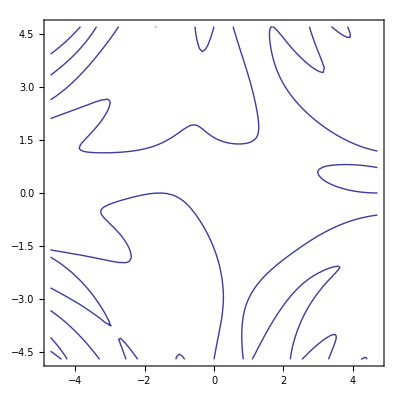

```mathematica
ContourPlot[Sin[x*y]==Sin[x]+Cos[y],{x,-3Pi/2,3Pi/2},{y,-3Pi/2,3Pi/2}]
```

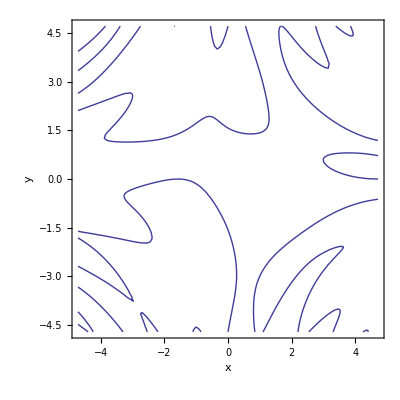

```mathematica
ContourPlot[Sin[x*y]==Sin[x]+Cos[y],{x,-3Pi/2,3Pi/2},{y,-3Pi/2,3Pi/2},AxesLabel-> {"x","y"}]
```

```mathematica
ContourPlot[Sin[x*y]==Sin[x]+Cos[y],{x,-3Pi/2,3Pi/2},{y,-3Pi/2,3Pi/2},AxesLabel-> {"x","y"},Axes-> True]
```

-Graphics-

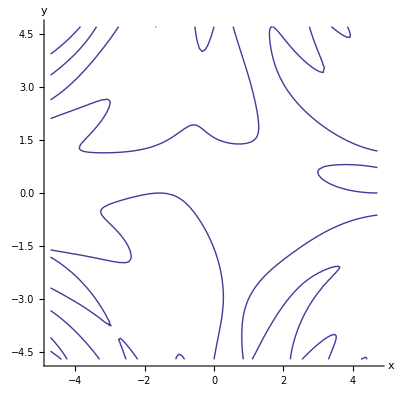

```mathematica
ContourPlot[Sin[x*y]==Sin[x]+Cos[y],{x,-3Pi/2,3Pi/2},{y,-3Pi/2,3Pi/2},AxesLabel-> {"x","y"},Axes-> True,Frame-> False]
```

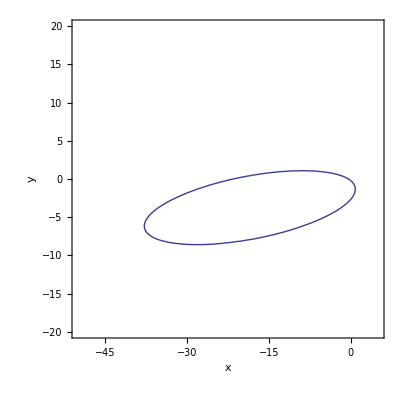

```mathematica
ContourPlot[x^2+16*y^2-4*x*y+22*x+46*y+9==0,{x,-50,5},{y,-20,20},AxesLabel-> {"x","y"},Axes-> True]
```

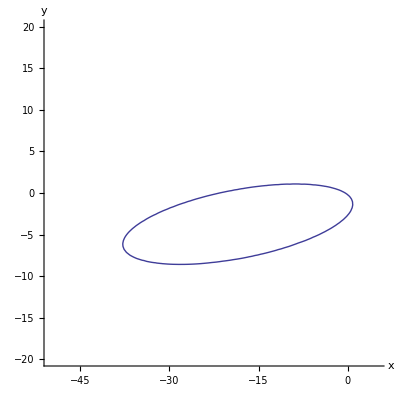

```mathematica
ContourPlot[x^2+16*y^2-4*x*y+22*x+46*y+9==0,{x,-50,5},{y,-20,20},AxesLabel-> {"x","y"},Axes-> True,Frame-> False]
```

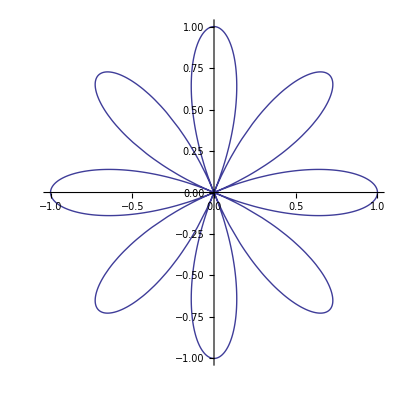

```mathematica
PolarPlot[Cos[4*θ],{θ,0,2π}]
```

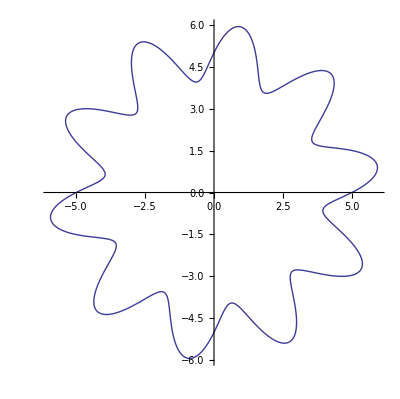

```mathematica
PolarPlot[5+Sin[10*θ],{θ,0,2π}]
```

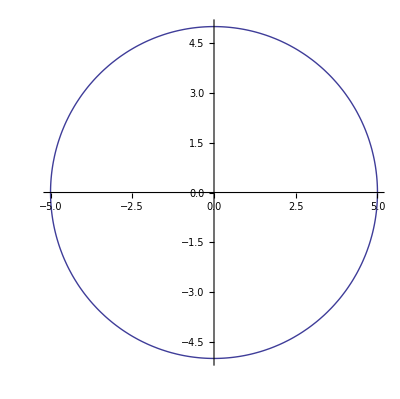

```mathematica
ParametricPlot[{5Cos[θ],5Sin[θ]},{θ,0,2π}]
```

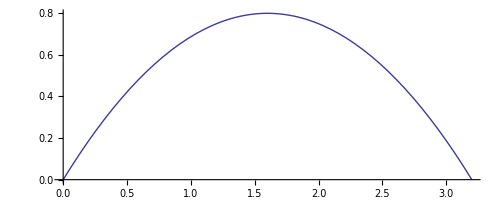

```mathematica
ParametricPlot[{4*t,4*t-5*t^2},{t,0,4/5}]
```

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π},AxesLabel-> {"X","Y"}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π},AxesLabel-> {"X","Y"},Mesh-> False]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x*y],{x,0,2π},{y,0,2π},AxesLabel-> {"X","Y"},Mesh-> False,PlotPoints-> 100]
```

-Graphics3D-

```mathematica
Plot3D[x^2+y^2,{x,-5,5},{y,-5,5},AxesLabel-> {"X","Y"}]
```

-Graphics3D-